```mathematica
FunctE[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))+((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]
```

-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))+((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]

```mathematica
FunctE1[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))]
```

-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))]

```mathematica
FunctE2[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]
```

-Im[((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]

```mathematica
GammaSMLO[omega_,gammarx_,omegarx_]=gammarx*omega/omegarx
```

(gammarx omega)/omegarx

```mathematica
MainDirecroty=NotebookDirectory[]
```

E:\Sasha\work\Students\Kucher\Cd106\

```mathematica
Filename="rsf106cd_eb2005.txt";
DataExp=ReadList[FileNameJoin[{MainDirecroty,Filename}],Number];
Ncolumbs=4;
Nmaxpoints1=Length[DataExp]/Ncolumbs-1;
X1aver=Table[DataExp[[Ncolumbs*i+2]],{i,0,Nmaxpoints1}];
Y1aver=Table[DataExp[[Ncolumbs*i+3]],{i,0,Nmaxpoints1}];
dY1aver=Table[DataExp[[Ncolumbs*i+4]],{i,0,Nmaxpoints1}];
Clear[DataExp]
```

```mathematica
Needs["ErrorBarPlots`"]
```

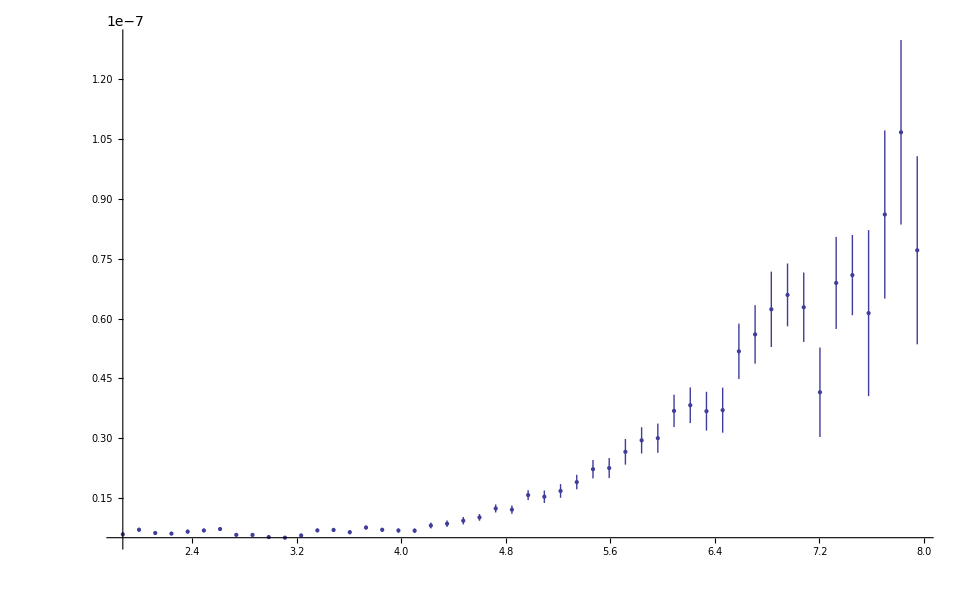

```mathematica
ErrorListPlot[{Transpose[{X1aver,Y1aver,dY1aver}]},PlotRange->All]
```

```mathematica
(* Fit  the cross section in the region [Ulow,Uupper] *)
```

```mathematica
Ulow=0.0;
Uupper=20.0;
Nlow=1;
Nupper=Length[Y1aver]
Do[If[X1aver[[i]]<Ulow,Nlow=i,Nlow=Nlow],{i,1,Length[Y1aver]}];
Do[If[X1aver[[i]]<Uupper,Nupper=i,Nupper=Nupper],{i,1,Length[Y1aver]}];
Nlow
Nupper
```

50

1

50

```mathematica
X1aver
```

{1.8715,1.9955,2.1195,2.2435,2.3675,2.4915,2.6155,2.7395,2.8635,2.9875,3.1115,3.2355,3.3595,3.4835,3.6075,3.7315,3.8555,3.9795,4.1035,4.2275,4.3515,4.4755,4.5995,4.7235,4.8475,4.9715,5.0955,5.2195,5.3435,5.4675,5.5915,5.7155,5.8395,5.9635,6.0875,6.2115,6.3355,6.4595,6.5835,6.7075,6.8315,6.9555,7.0795,7.2035,7.3275,7.4515,7.5755,7.6995,7.8235,7.9475}

```mathematica
Y1aver
```

{5.86666×10^-9,7.02504×10^-9,6.2019×10^-9,6.06183×10^-9,6.54816×10^-9,6.84132×10^-9,7.19793×10^-9,5.73946×10^-9,5.72482×10^-9,5.18361×10^-9,5.02909×10^-9,5.5857×10^-9,6.85462×10^-9,6.9606×10^-9,6.402×10^-9,7.57172×10^-9,7.01079×10^-9,6.8324×10^-9,6.78773×10^-9,8.08297×10^-9,8.54007×10^-9,9.28938×10^-9,1.01168×10^-8,1.23644×10^-8,1.20622×10^-8,1.57093×10^-8,1.53075×10^-8,1.67577×10^-8,1.89868×10^-8,2.22119×10^-8,2.24966×10^-8,2.65748×10^-8,2.94484×10^-8,2.99948×10^-8,3.68432×10^-8,3.8259×10^-8,3.6764×10^-8,3.70234×10^-8,5.17768×10^-8,5.6032×10^-8,6.23217×10^-8,6.59325×10^-8,6.28414×10^-8,4.15124×10^-8,6.89378×10^-8,7.08992×10^-8,6.13677×10^-8,8.61076×10^-8,1.06736×10^-7,7.71329×10^-8}

```mathematica
dY1aver
```

{4.68094×10^-10,4.88686×10^-10,4.35272×10^-10,4.01826×10^-10,4.8507×10^-10,4.43339×10^-10,3.94548×10^-10,3.41589×10^-10,4.08984×10^-10,3.69075×10^-10,3.34294×10^-10,4.37803×10^-10,4.28379×10^-10,5.218×10^-10,4.97133×10^-10,4.97538×10^-10,4.73024×10^-10,5.04021×10^-10,5.41605×10^-10,7.29275×10^-10,8.04627×10^-10,9.34743×10^-10,8.47702×10^-10,1.01235×10^-9,1.04849×10^-9,1.23642×10^-9,1.56393×10^-9,1.70729×10^-9,1.82082×10^-9,2.30575×10^-9,2.51248×10^-9,3.22104×10^-9,3.288×10^-9,3.66107×10^-9,4.05941×10^-9,4.46552×10^-9,4.8696×10^-9,5.64992×10^-9,6.95287×10^-9,7.32759×10^-9,9.45362×10^-9,7.87577×10^-9,8.70532×10^-9,1.12174×10^-8,1.15454×10^-8,1.00584×10^-8,2.08231×10^-8,2.1092×10^-8,2.31546×10^-8,2.35962×10^-8}

{4.68094×10^-10,4.88686×10^-10,4.35272×10^-10,4.01826×10^-10,4.8507×10^-10,4.43339×10^-10,3.94548×10^-10,3.41589×10^-10,4.08984×10^-10,3.69075×10^-10,3.34294×10^-10,4.37803×10^-10,4.28379×10^-10,5.218×10^-10,4.97133×10^-10,4.97538×10^-10,4.73024×10^-10,5.04021×10^-10,5.41605×10^-10,7.29275×10^-10,8.04627×10^-10,9.34743×10^-10,8.47702×10^-10,1.01235×10^-9,1.04849×10^-9,1.23642×10^-9,1.56393×10^-9,1.70729×10^-9,1.82082×10^-9,2.30575×10^-9,2.51248×10^-9,3.22104×10^-9,3.288×10^-9,3.66107×10^-9,4.05941×10^-9,4.46552×10^-9,4.8696×10^-9,5.64992×10^-9,6.95287×10^-9,7.32759×10^-9,9.45362×10^-9,7.87577×10^-9,8.70532×10^-9,1.12174×10^-8,1.15454×10^-8,1.00584×10^-8,2.08231×10^-8,2.1092×10^-8,2.31546×10^-8,2.35962×10^-8}

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {5.48012×10^-13, 0.00201239, 2.68854×10^-13}, is returned.

FittedModel[-Im[(0.0000102851+((0.+«1») «5»)/(«18»+«1»-(«5»)^2))/(143.896+(0.+«1») «5»-«1»+(«20» («5»)^2)/(«18»+«1»-(«5»)^2))+(«23»«1»«1»)/(«1»)]]

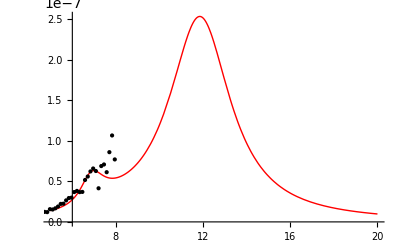

11.9957

6.84549

3.04692

0.934635

0.376258

0.00320704

0.000568008

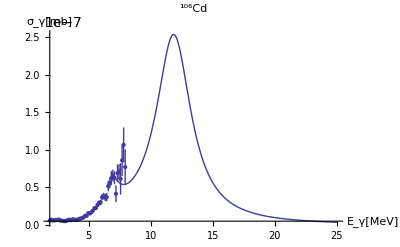

E:\Sasha\work\Students\Kucher\Cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {"ParameterTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 11.9957 | 38.0936 | 0.3149 | 0.754361
omega2p | 6.84549 | 0.931569 | 7.34835 | 4.04236×10^-9
Gamma1p | 3.04692 | 149.094 | 0.0204362 | 0.98379
Gamma2p | 0.934635 | 9.63743 | 0.0969797 | 0.923193
Gamma12p | 0.376258 | 10.5371 | 0.0357078 | 0.971681
Z10 | 0.00320704 | 0.0939929 | 0.03412 | 0.972939
Z20 | 0.000568008 | 0.00121427 | 0.467777 | 0.642306

FittedModel::constr: The property values {"ParameterTableEntries"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{11.9957,38.0936,0.3149,0.754361},{6.84549,0.931569,7.34835,4.04236×10^-9},{3.04692,149.094,0.0204362,0.98379},{0.934635,9.63743,0.0969797,0.923193},{0.376258,10.5371,0.0357078,0.971681},{0.00320704,0.0939929,0.03412,0.972939},{0.000568008,0.00121427,0.467777,0.642306}}

7.64758

7.64758

```mathematica
(*TSE  !!!!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,Nlow,Nmaxpointstemp}];
FordY1aver=Table[dY1aver[[i]],{i,Nlow,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,Nlow,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,Nlow,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,Gamma2p,Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0
},{{omega1p,12},{omega2p,7},{Gamma1p,3},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEgam[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEgam=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{4.68094×10^-10,4.88686×10^-10,4.35272×10^-10,4.01826×10^-10,4.8507×10^-10,4.43339×10^-10,3.94548×10^-10,3.41589×10^-10,4.08984×10^-10,3.69075×10^-10,3.34294×10^-10,4.37803×10^-10,4.28379×10^-10,5.218×10^-10,4.97133×10^-10,4.97538×10^-10,4.73024×10^-10,5.04021×10^-10,5.41605×10^-10,7.29275×10^-10,8.04627×10^-10,9.34743×10^-10,8.47702×10^-10,1.01235×10^-9,1.04849×10^-9,1.23642×10^-9,1.56393×10^-9,1.70729×10^-9,1.82082×10^-9,2.30575×10^-9,2.51248×10^-9,3.22104×10^-9,3.288×10^-9,3.66107×10^-9,4.05941×10^-9,4.46552×10^-9,4.8696×10^-9,5.64992×10^-9,6.95287×10^-9,7.32759×10^-9,9.45362×10^-9,7.87577×10^-9,8.70532×10^-9,1.12174×10^-8,1.15454×10^-8,1.00584×10^-8,2.08231×10^-8,2.1092×10^-8,2.31546×10^-8,2.35962×10^-8}

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {9.77033×10^-13, 0.00249304, 5.0151×10^-13}, is returned.

FittedModel[-Im[(5.69326×10^-7)/(51.6162+(0.+1.66633 ⅈ) omega-omega^2)+0.0000292374/(«19»+(«1») «5»-omega^2)]]

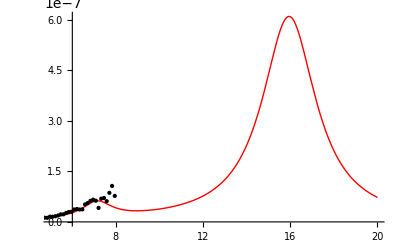

16.0131

7.18444

3.00481

1.66633

0.00540717

0.000754537

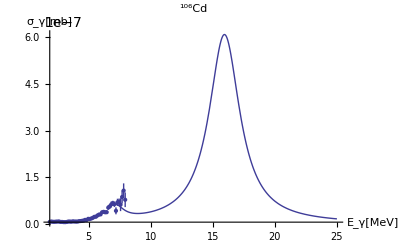

E:\Sasha\work\Students\Kucher\Cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {"ParameterTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 16.0131 | 178.42 | 0.0897494 | 0.928894
omega2p | 7.18444 | 0.740791 | 9.69834 | 1.70366×10^-12
Gamma1p | 3.00481 | 1817.66 | 0.00165312 | 0.998688
Gamma2p | 1.66633 | 1.55632 | 1.07069 | 0.290149
Z10 | 0.00540717 | 1.75521 | 0.00308064 | 0.997556
Z20 | 0.000754537 | 0.000861025 | 0.876324 | 0.385613

FittedModel::constr: The property values {"ParameterTableEntries"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{16.0131,178.42,0.0897494,0.928894},{7.18444,0.740791,9.69834,1.70366×10^-12},{3.00481,1817.66,0.00165312,0.998688},{1.66633,1.55632,1.07069,0.290149},{0.00540717,1.75521,0.00308064,0.997556},{0.000754537,0.000861025,0.876324,0.385613}}

7.63988

7.63988

```mathematica
(*independent Gamma12p=0 !!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,Gamma2p,0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEgam0[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEgam0=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{4.68094×10^-10,4.88686×10^-10,4.35272×10^-10,4.01826×10^-10,4.8507×10^-10,4.43339×10^-10,3.94548×10^-10,3.41589×10^-10,4.08984×10^-10,3.69075×10^-10,3.34294×10^-10,4.37803×10^-10,4.28379×10^-10,5.218×10^-10,4.97133×10^-10,4.97538×10^-10,4.73024×10^-10,5.04021×10^-10,5.41605×10^-10,7.29275×10^-10,8.04627×10^-10,9.34743×10^-10,8.47702×10^-10,1.01235×10^-9,1.04849×10^-9,1.23642×10^-9,1.56393×10^-9,1.70729×10^-9,1.82082×10^-9,2.30575×10^-9,2.51248×10^-9,3.22104×10^-9,3.288×10^-9,3.66107×10^-9,4.05941×10^-9,4.46552×10^-9,4.8696×10^-9,5.64992×10^-9,6.95287×10^-9,7.32759×10^-9,9.45362×10^-9,7.87577×10^-9,8.70532×10^-9,1.12174×10^-8,1.15454×10^-8,1.00584×10^-8,2.08231×10^-8,2.1092×10^-8,2.31546×10^-8,2.35962×10^-8}

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.12018×10^-12, 0.00671722, 4.6034×10^-13}, is returned.

FittedModel[-Im[(2.22282×10^-7+((0.+«1») omega)/(«18»+«1»-(«5»)^2))/(37.7887+ⅈ («1») omega-«1»+(«19» («5»)^2)/(«18»+«1»-(«5»)^2))+(«23»«1»«1»)/(«1»)]]

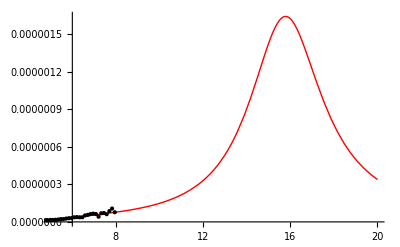

16.1267

6.14725

2.32265

1.18203

1.92135

0.0103444

0.000471468

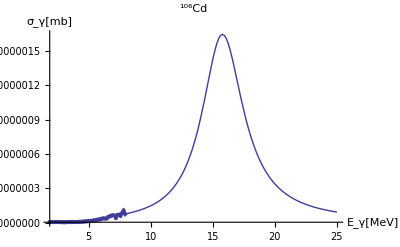

E:\Sasha\work\Students\Kucher\Cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {"ParameterTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 16.1267 | 40.0143 | 0.403024 | 0.688927
omega2p | 6.14725 | 1.65586 | 3.71242 | 0.000586012
Gamma1p | 2.32265 | 26.2465 | 0.0884936 | 0.929895
Gamma2p | 1.18203 | 4.65421 | 0.253971 | 0.800729
Gamma12p | 1.92135 | 7.79503 | 0.246485 | 0.80648
Z10 | 0.0103444 | 0.0385801 | 0.268128 | 0.789883
Z20 | 0.000471468 | 0.000897068 | 0.525566 | 0.60189

FittedModel::constr: The property values {"ParameterTableEntries"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{16.1267,40.0143,0.403024,0.688927},{6.14725,1.65586,3.71242,0.000586012},{2.32265,26.2465,0.0884936,0.929895},{1.18203,4.65421,0.253971,0.800729},{1.92135,7.79503,0.246485,0.80648},{0.0103444,0.0385801,0.268128,0.789883},{0.000471468,0.000897068,0.525566,0.60189}}

6.39711

6.39711

```mathematica
(*TSE SMLO GDR and PDR *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],GammaSMLO[omega,Gamma2p,omega2p],Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRsmloGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRsmloGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{4.68094×10^-10,4.88686×10^-10,4.35272×10^-10,4.01826×10^-10,4.8507×10^-10,4.43339×10^-10,3.94548×10^-10,3.41589×10^-10,4.08984×10^-10,3.69075×10^-10,3.34294×10^-10,4.37803×10^-10,4.28379×10^-10,5.218×10^-10,4.97133×10^-10,4.97538×10^-10,4.73024×10^-10,5.04021×10^-10,5.41605×10^-10,7.29275×10^-10,8.04627×10^-10,9.34743×10^-10,8.47702×10^-10,1.01235×10^-9,1.04849×10^-9,1.23642×10^-9,1.56393×10^-9,1.70729×10^-9,1.82082×10^-9,2.30575×10^-9,2.51248×10^-9,3.22104×10^-9,3.288×10^-9,3.66107×10^-9,4.05941×10^-9,4.46552×10^-9,4.8696×10^-9,5.64992×10^-9,6.95287×10^-9,7.32759×10^-9,9.45362×10^-9,7.87577×10^-9,8.70532×10^-9,1.12174×10^-8,1.15454×10^-8,1.00584×10^-8,2.08231×10^-8,2.1092×10^-8,2.31546×10^-8,2.35962×10^-8}

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {9.97935×10^-12, 0.00102489, 5.35883×10^-12}, is returned.

FittedModel[-Im[(0.0000566643+((0.+«1») «5»)/(«19»+«1»-(«5»)^2))/(249.53+ⅈ («1») omega«1»«1»+(«18» («5»)^2)/(«19»+(«1») «5»-(«5»)^2))+(«1»)/(«1»)]]

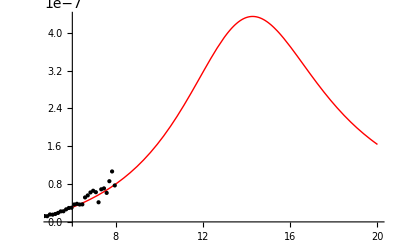

15.7965

3.97244

5.43708

0.338937

4.13014

0.00752757

5.86338×10^-13

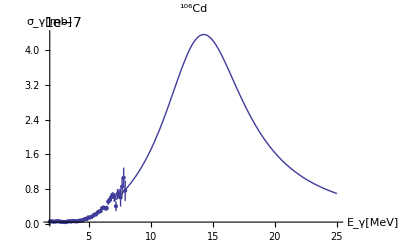

E:\Sasha\work\Students\Kucher\Cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {"ParameterTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 15.7965 | 9.34365 | 1.69061 | 0.0981482
omega2p | 3.97244 | 2.26533 | 1.75358 | 0.0866285
Gamma1p | 5.43708 | 74.7124 | 0.0727735 | 0.942324
Gamma2p | 0.338937 | 8.77922 | 0.0386068 | 0.969383
Gamma12p | 4.13014 | 7.68002 | 0.537777 | 0.593504
Z10 | 0.00752757 | 0.0243281 | 0.309419 | 0.758497
Z20 | 5.86338×10^-13 | 0.00093451 | 6.27428×10^-10 | 1

FittedModel::constr: The property values {"ParameterTableEntries"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{15.7965,9.34365,1.69061,0.0981482},{3.97244,2.26533,1.75358,0.0866285},{5.43708,74.7124,0.0727735,0.942324},{0.338937,8.77922,0.0386068,0.969383},{4.13014,7.68002,0.537777,0.593504},{0.00752757,0.0243281,0.309419,0.758497},{5.86338×10^-13,0.00093451,6.27428×10^-10,1}}

1.65337

1.65337

```mathematica
(*TSE SMLO GDR and PDG G=const !!!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],Gamma2p,Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,omega1p>0,omega2p>0,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRconsGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRconsGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{4.68094×10^-10,4.88686×10^-10,4.35272×10^-10,4.01826×10^-10,4.8507×10^-10,4.43339×10^-10,3.94548×10^-10,3.41589×10^-10,4.08984×10^-10,3.69075×10^-10,3.34294×10^-10,4.37803×10^-10,4.28379×10^-10,5.218×10^-10,4.97133×10^-10,4.97538×10^-10,4.73024×10^-10,5.04021×10^-10,5.41605×10^-10,7.29275×10^-10,8.04627×10^-10,9.34743×10^-10,8.47702×10^-10,1.01235×10^-9,1.04849×10^-9,1.23642×10^-9,1.56393×10^-9,1.70729×10^-9,1.82082×10^-9,2.30575×10^-9,2.51248×10^-9,3.22104×10^-9,3.288×10^-9,3.66107×10^-9,4.05941×10^-9,4.46552×10^-9,4.8696×10^-9,5.64992×10^-9,6.95287×10^-9,7.32759×10^-9,9.45362×10^-9,7.87577×10^-9,8.70532×10^-9,1.12174×10^-8,1.15454×10^-8,1.00584×10^-8,2.08231×10^-8,2.1092×10^-8,2.31546×10^-8,2.35962×10^-8}

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {3.39365×10^-13, 0.00216774, 2.20002×10^-13}, is returned.

FittedModel[-Im[(4.29855×10^-7+((0.+«1») omega)/(«19»+«1»-(«5»)^2))/(47.5455+ⅈ («1») omega«1»«1»+(«20» («5»)^2)/(«19»+(«1») «5»-(«5»)^2))+(«1»)/(«1»)]]

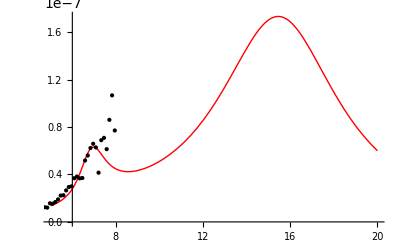

15.8509

6.89533

6.11721

0.878959

0.615987

0.00425731

0.000655633

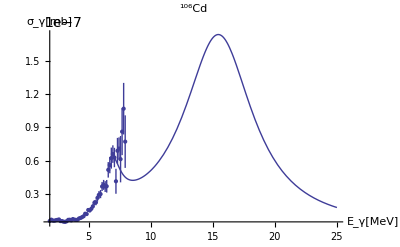

E:\Sasha\work\Students\Kucher\Cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {"ParameterTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 15.8509 | 547.766 | 0.0289374 | 0.977048
omega2p | 6.89533 | 6.88964 | 1.00082 | 0.32251
Gamma1p | 6.11721 | 1342.31 | 0.00455723 | 0.996385
Gamma2p | 0.878959 | 80.2209 | 0.0109567 | 0.991309
Gamma12p | 0.615987 | 78.736 | 0.00782344 | 0.993794
Z10 | 0.00425731 | 0.750331 | 0.0056739 | 0.995499
Z20 | 0.000655633 | 0.00685604 | 0.0956286 | 0.92426

FittedModel::constr: The property values {"ParameterTableEntries"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{15.8509,547.766,0.0289374,0.977048},{6.89533,6.88964,1.00082,0.32251},{6.11721,1342.31,0.00455723,0.996385},{0.878959,80.2209,0.0109567,0.991309},{0.615987,78.736,0.00782344,0.993794},{0.00425731,0.750331,0.0056739,0.995499},{0.000655633,0.00685604,0.0956286,0.92426}}

7.14874

7.14874

```mathematica
(*TSE SMLO PDR and GDR G=const *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,GammaSMLO[omega,Gamma2p,omega2p],Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRsmloGDRcons[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRsmloGDRcons=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{4.68094×10^-10,4.88686×10^-10,4.35272×10^-10,4.01826×10^-10,4.8507×10^-10,4.43339×10^-10,3.94548×10^-10,3.41589×10^-10,4.08984×10^-10,3.69075×10^-10,3.34294×10^-10,4.37803×10^-10,4.28379×10^-10,5.218×10^-10,4.97133×10^-10,4.97538×10^-10,4.73024×10^-10,5.04021×10^-10,5.41605×10^-10,7.29275×10^-10,8.04627×10^-10,9.34743×10^-10,8.47702×10^-10,1.01235×10^-9,1.04849×10^-9,1.23642×10^-9,1.56393×10^-9,1.70729×10^-9,1.82082×10^-9,2.30575×10^-9,2.51248×10^-9,3.22104×10^-9,3.288×10^-9,3.66107×10^-9,4.05941×10^-9,4.46552×10^-9,4.8696×10^-9,5.64992×10^-9,6.95287×10^-9,7.32759×10^-9,9.45362×10^-9,7.87577×10^-9,8.70532×10^-9,1.12174×10^-8,1.15454×10^-8,1.00584×10^-8,2.08231×10^-8,2.1092×10^-8,2.31546×10^-8,2.35962×10^-8}

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {2.92135×10^-13, 0.000462581, 1.3589×10^-13}, is returned.

FittedModel[-Im[(1.52533×10^-7)/(47.6535-(1.-0.0990338 ⅈ) («5»)^2)+0.000125635/(299.126-«1»)]]

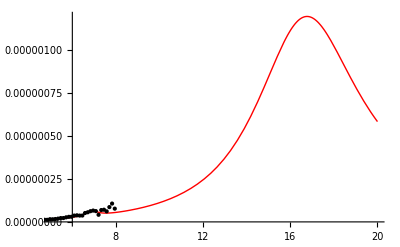

17.2953

6.90315

6.26566

0.683645

0.0112087

0.000390555

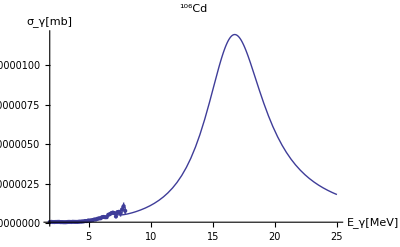

E:\Sasha\work\Students\Kucher\Cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {"ParameterTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 17.2953 | 21.3035 | 0.811852 | 0.421247
omega2p | 6.90315 | 0.319795 | 21.5862 | 4.85935×10^-25
Gamma1p | 6.26566 | 585.335 | 0.0107044 | 0.991508
Gamma2p | 0.683645 | 1.02584 | 0.666427 | 0.508618
Z10 | 0.0112087 | 0.551982 | 0.0203063 | 0.983891
Z20 | 0.000390555 | 0.00033169 | 1.17747 | 0.245337

FittedModel::constr: The property values {"ParameterTableEntries"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{17.2953,21.3035,0.811852,0.421247},{6.90315,0.319795,21.5862,4.85935×10^-25},{6.26566,585.335,0.0107044,0.991508},{0.683645,1.02584,0.666427,0.508618},{0.0112087,0.551982,0.0203063,0.983891},{0.000390555,0.00033169,1.17747,0.245337}}

15.621

15.621

```mathematica
(*independent Gamma12p=0, SMLO GDR and PDG *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],GammaSMLO[omega,Gamma2p,omega2p],0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRsmloGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRsmloGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{4.68094×10^-10,4.88686×10^-10,4.35272×10^-10,4.01826×10^-10,4.8507×10^-10,4.43339×10^-10,3.94548×10^-10,3.41589×10^-10,4.08984×10^-10,3.69075×10^-10,3.34294×10^-10,4.37803×10^-10,4.28379×10^-10,5.218×10^-10,4.97133×10^-10,4.97538×10^-10,4.73024×10^-10,5.04021×10^-10,5.41605×10^-10,7.29275×10^-10,8.04627×10^-10,9.34743×10^-10,8.47702×10^-10,1.01235×10^-9,1.04849×10^-9,1.23642×10^-9,1.56393×10^-9,1.70729×10^-9,1.82082×10^-9,2.30575×10^-9,2.51248×10^-9,3.22104×10^-9,3.288×10^-9,3.66107×10^-9,4.05941×10^-9,4.46552×10^-9,4.8696×10^-9,5.64992×10^-9,6.95287×10^-9,7.32759×10^-9,9.45362×10^-9,7.87577×10^-9,8.70532×10^-9,1.12174×10^-8,1.15454×10^-8,1.00584×10^-8,2.08231×10^-8,2.1092×10^-8,2.31546×10^-8,2.35962×10^-8}

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.82018×10^-12, 0.0000102411, 6.85223×10^-13}, is returned.

FittedModel[-Im[(2.42354×10^-6)/(72.1944+(0.+3.10433 ⅈ) omega-omega^2)+(1.23088×10^-20)/(262.306-«1»)]]

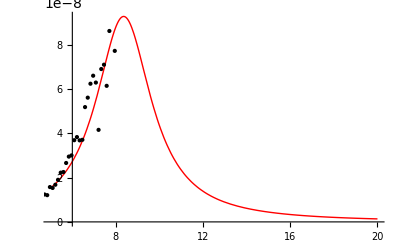

16.1959

8.49673

6.03691

3.10433

1.10945×10^-10

0.00155677

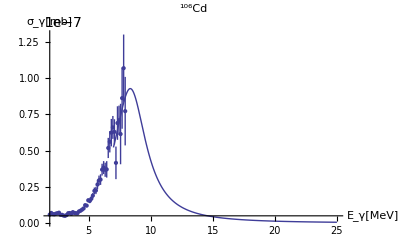

E:\Sasha\work\Students\Kucher\Cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {"ParameterTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 16.1959 | 2.32822×10^-6 | 6.95631×10^6 | 1.47578×10^-266
omega2p | 8.49673 | 0.83913 | 10.1256 | 4.53931×10^-13
Gamma1p | 6.03691 | 1.53107×10^-10 | 3.94293×10^10 | 1.04148759418527×10^-431
Gamma2p | 3.10433 | 0.83697 | 3.70901 | 0.000580323
Z10 | 1.10945×10^-10 | 3094.35 | 3.58541×10^-14 | 1
Z20 | 0.00155677 | 0.000434254 | 3.58493 | 0.000840018

FittedModel::constr: The property values {"ParameterTableEntries"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{16.1959,2.32822×10^-6,6.95631×10^6,1.47578×10^-266},{8.49673,0.83913,10.1256,4.53931×10^-13},{6.03691,1.53107×10^-10,3.94293×10^10,1.04148759418527×10^-431},{3.10433,0.83697,3.70901,0.000580323},{1.10945×10^-10,3094.35,3.58541×10^-14,1},{0.00155677,0.000434254,3.58493,0.000840018}}

9.42743

9.42743

```mathematica
(*independent Gamma12p=0, SMLO GDR and PDG G=const !!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],Gamma2p,0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRconsGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRconsGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{4.68094×10^-10,4.88686×10^-10,4.35272×10^-10,4.01826×10^-10,4.8507×10^-10,4.43339×10^-10,3.94548×10^-10,3.41589×10^-10,4.08984×10^-10,3.69075×10^-10,3.34294×10^-10,4.37803×10^-10,4.28379×10^-10,5.218×10^-10,4.97133×10^-10,4.97538×10^-10,4.73024×10^-10,5.04021×10^-10,5.41605×10^-10,7.29275×10^-10,8.04627×10^-10,9.34743×10^-10,8.47702×10^-10,1.01235×10^-9,1.04849×10^-9,1.23642×10^-9,1.56393×10^-9,1.70729×10^-9,1.82082×10^-9,2.30575×10^-9,2.51248×10^-9,3.22104×10^-9,3.288×10^-9,3.66107×10^-9,4.05941×10^-9,4.46552×10^-9,4.8696×10^-9,5.64992×10^-9,6.95287×10^-9,7.32759×10^-9,9.45362×10^-9,7.87577×10^-9,8.70532×10^-9,1.12174×10^-8,1.15454×10^-8,1.00584×10^-8,2.08231×10^-8,2.1092×10^-8,2.31546×10^-8,2.35962×10^-8}

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {7.45327×10^-13, 0.000250452, 2.79917×10^-13}, is returned.

FittedModel[-Im[0.0000174501/(250.995+(0.+6.19183 ⅈ) omega-omega^2)+(4.32533×10^-7)/(«19»-(1.-«1») «1»)]]

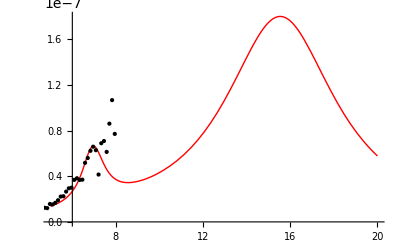

15.8428

7.00717

6.19183

1.27116

0.00417733

0.000657672

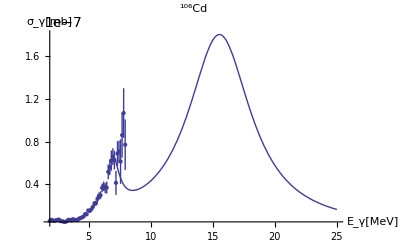

E:\Sasha\work\Students\Kucher\Cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {"ParameterTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 15.8428 | 112.598 | 0.140703 | 0.888747
omega2p | 7.00717 | 0.367847 | 19.0491 | 7.07011×10^-23
Gamma1p | 6.19183 | 458.21 | 0.0135131 | 0.98928
Gamma2p | 1.27116 | 0.91766 | 1.38522 | 0.172968
Z10 | 0.00417733 | 0.213506 | 0.0195654 | 0.984479
Z20 | 0.000657672 | 0.000403427 | 1.63021 | 0.110195

FittedModel::constr: The property values {"ParameterTableEntries"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{15.8428,112.598,0.140703,0.888747},{7.00717,0.367847,19.0491,7.07011×10^-23},{6.19183,458.21,0.0135131,0.98928},{1.27116,0.91766,1.38522,0.172968},{0.00417733,0.213506,0.0195654,0.984479},{0.000657672,0.000403427,1.63021,0.110195}}

7.42797

7.42797

```mathematica
(*independent Gamma12p=0, SMLO PDR and GDR G=const *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,GammaSMLO[omega,Gamma2p,omega2p],0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRsmloGDRcons[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRsmloGDRcons=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

```mathematica
"E:\\Sasha\\work\\Students\\Kucher\\Cd106\\FigSigmaFit106Cd.eps"
```

E:\Sasha\work\Students\Kucher\Cd106\FigSigmaFit106Cd.eps

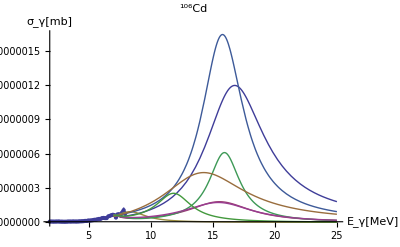

```mathematica
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[{ResponseFuncPDRsmloGDRsmlo[x],ResponseFuncPDRsmloGDRcons[x],ResponseFuncPDRconsGDRsmlo[x],ResponseFuncTSEgam0[x],ResponseFuncTSEPDRsmloGDRsmlo[x],ResponseFuncTSEPDRsmloGDRcons[x],ResponseFuncTSEPDRconsGDRsmlo[x],ResponseFuncTSEgam[x]},{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
```

```mathematica
Chi2PDRsmloGDRsmlo
Chi2PDRsmloGDRcons
Chi2PDRconsGDRsmlo
Chi2TSEgam0
Chi2TSEPDRsmloGDRsmlo
Chi2TSEPDRsmloGDRcons
Chi2TSEPDRconsGDRsmlo
Chi2TSEgam
```

15.621

7.42797

9.42743

7.63988

6.39711

7.14874

1.65337

7.64758